# Skeleton-based Analysis of Melt Network

## Functions

```mathematica
Clear["Global`*"];
```

readSkel[path] reads .ply skeleton file as a table and returns points, lines and radius:

```mathematica
readSkel:= Function[path, 
	rawData = Import[path,"Table"];
	numOfPoints = rawData⟦3,3⟧;
	numOfEdges = rawData⟦9,3⟧;
	dataTable = rawData⟦15;;,;;⟧;
	
	burnTime = dataTable⟦;;numOfPoints,1⟧;
	Points = dataTable⟦;;numOfPoints,3;;5⟧;
	Lines = dataTable⟦numOfPoints+1;;⟧ + 1;
	Radius = dataTable⟦;;numOfPoints,2⟧;
	{Points,Lines,Radius,burnTime}
]
```

linesToGraph[lines] construct a graph based on the lines

```mathematica
linesToGraph:=Function[{lines},
	graph=Graph[Table[lines⟦i,1⟧<->lines⟦i,2⟧,{i,1,Dimensions[lines]⟦1⟧}]]
]
```

getJunctions[graph] collect all junction nodes(degree >= 3) and their degree from a graph

```mathematica
a=Graph[{1<->2,1<->3,6<->2}];
VertexList[a]
```

{1,2,3,6}

```mathematica
getJunctions:=Function[{graph},
	ans={};
	vertices=VertexList[graph];
	Do[
		degree = VertexDegree[graph,vertex];
		If[degree>2,AppendTo[ans,{vertex,degree}]];
	,{vertex,vertices}];
	ans
]
```

InitJG[points, lines, radius] generates a list of junctions and a simplified graph based on these junctions
	Inputs: 
		points: a list of all points in skeleton
		lines: a list of all lines in skeleton
		radius: a list of radius of each point in skeleton
	Returns:
		junctionDataTable: a list of all basic junctions {identifier, degree, cluster, coordinate, radius}
		simplifiedG: a simplified graph which eliminates all vertices with degree of 2

```mathematica
initJG:= Function[{points, lines, radius,burntime},
	skelGraph = linesToGraph[lines];
	Print["Initial graph built!"];
	simplifiedG = simplifyGraph[skelGraph];
	Print["simplified graph done!"];
	junctions = getJunctions[skelGraph];
	junctionsDataTable = Table[{junctions⟦i,1⟧,junctions⟦i,2⟧,{{junctions⟦i,1⟧,points⟦junctions⟦i,1⟧,;;⟧,radius⟦junctions⟦i,1⟧⟧}},points⟦junctions⟦i,1⟧,;;⟧,radius⟦junctions⟦i,1⟧⟧,burntime⟦junctions⟦i,1⟧⟧},{i,Dimensions[junctions]⟦1⟧}];	
	(*junctionsDataTable = Select[junctionsDataTable,#⟦6⟧ > 1 &];*)
	Print["Basic junctions computed!"];
	{junctionsDataTable, simplifiedG}
]
```

```mathematica
computeAngle:=Function[{vec1,vec2},
	If[Norm[vec1]*Norm[vec2] == 0, 
		angle = 0,
		cosValue=vec1.vec2/(Norm[vec1]*Norm[vec2]);
		angle = ArcCos[cosValue]/(2*Pi) * 360;
	];
	angle
]
```

```mathematica
computeStdAngle:=Function[d,
	points = SpherePoints[d];
	minAngle = 180;
	For[i=1, i≤Length[points] - 1,i++,
		For[j =i+1, j≤ Length[points], j++,
			theAngle = computeAngle[points⟦i⟧-{0,0,0},points⟦j⟧-{0,0,0}];
			minAngle = Min[theAngle, minAngle]; 
		]
	];
	minAngle
]
```

```mathematica
angleScore:=Function[{allPoints,c,d,stdAngle},
	edges=c⟦7⟧;
	aScore = -100;
	n=Length[edges];
	For[i=1,i≤n-1,i++,
		edge1=edges⟦i⟧;
		point11=allPoints⟦edge1⟦1⟧,;;⟧;
		point12=allPoints⟦edge1⟦2⟧,;;⟧;
		vec1=point12-point11;
		For[j=i+1,j≤n,j++,
			edge2=edges⟦j⟧;
			point21=allPoints⟦edge2⟦1⟧,;;⟧;
			point22=allPoints⟦edge2⟦2⟧,;;⟧;
			vec2=point22-point21;
			theAngle=computeAngle[vec1,vec2];
			aScore = Max[aScore, Abs[theAngle - stdAngle] / 15];
		];
	];
	aScore
]
```

```mathematica
clusterAngleScore:= Function[{simplifiedG,allPoints, c1, c2, d},
	stdAngle = computeStdAngle[d];
	aScore1 = angleScore[allPoints, c1, d, stdAngle];
	aScore2 = angleScore[allPoints, c2, d, stdAngle];
	worstScore = Max[aScore1, aScore2];
	worstScore
]
```

distanceScore[ball1, ball2] computes the score which tell whether the two balls should be merged
	ball1: {identifier, {x1,y1,z1}, r1} 
	ball2: {identifier, {x2,y2,z2}, r2}

```mathematica
distanceScore := Function[{ball1, ball2},
	r1 = Max[ball1⟦3⟧,ball2⟦3⟧];
	r2 = Min[ball1⟦3⟧,ball2⟦3⟧];
	d = EuclideanDistance[ball1⟦2⟧, ball2⟦2⟧];
	(*score = If[r2==0, If[r1==0,d, (-r1+d)/r1],(-r1 - r2 + d)/r2];*)
	score = If[r2==0, -r1+d,(-r1 - r2 + d)/(2*r2)];
	score
]
```

clusterDistanceScore[simplifiedG,c1,c2] computes the distance score between cluster c1 and cluster c2
Inputs:
	c1, c2: a merged junction {identifier, degree, cluster, coordinate, radius}
Return:
	worstScore: the worst distance score among all scores between each ball in  c1 and each ball in c2

```mathematica
clusterDistanceScore:= Function[{initSimplifiedG,c1,c2},
	worstScore = -100;
	ballList1 = c1⟦3⟧;
	ballList2 = c2⟦3⟧;
	For[i=1, i≤Length[ballList1],i++,
		For[j=1, j≤Length[ballList2],j++,
			(*If[EdgeQ[initSimplifiedG,ballList1⟦i,1⟧<->ballList2⟦j,1⟧],*)
				worstScore = Max[worstScore, distanceScore[ballList1⟦i⟧, ballList2⟦j⟧]];
			(*]*)
		]
	];
	worstScore
]
```

clusterMergeScore[c1,c2] computes the worst score between cluster c1 and cluster c2
Inputs:
	c1, c2: a merged junction {identifier, degree, cluster, coordinate, radius}
Return:
	worstScore: the minimum score among all scores between each ball in  c1 and each ball in c2

```mathematica
clusterMergeScore:= Function[{simplifiedG,,initSimpleG,allPoints,c1,c2},
	dScore = clusterDistanceScore[initSimpleG, c1, c2];
	innerDegree = Length[EdgeList[simplifiedG,c1⟦1⟧<->c2⟦1⟧]];
	(*d = c1⟦2⟧ + c2⟦2⟧ - innerDegree * 2;*)
	d = VertexDegree[simplifiedG, c1⟦1⟧] + VertexDegree[simplifiedG, c2⟦1⟧] - innerDegree * 2;
	aScore = clusterAngleScore[simplifiedG,allPoints,c1,c2,d];
	totalScore=(d-1)/d*dScore + 1/d*aScore;
	{dScore, aScore, totalScore}
]
```

```mathematica
isMergable:=Function[{dScore},
	If[dScore ≤ 1, 
		True, 
		False
	]
]
```

```mathematica
deleteNode := Function[{graph, v},
	resGraph = graph;
	If[VertexDegree[graph, v] ≠ 2, Throw[resGraph]];
	
	neighbors = AdjacencyList[resGraph,v];
	v1 = neighbors⟦1⟧;
	v2 = If[Length[neighbors] == 2,neighbors⟦2⟧, neighbors⟦1⟧];
	
	resGraph = VertexDelete[resGraph, v];
	resGraph = EdgeAdd[resGraph,v1<->v2];
	resGraph
]
```

```mathematica
simplifyGraph := Function[{skelGraph},
	g = skelGraph;
	nodesDeg2 = Pick[VertexList[g], VertexDegree[g], 2];
	
	While[Length[nodesDeg2] > 0,
		g = Catch[deleteNode[g, nodesDeg2⟦1⟧]];
		nodesDeg2 = Drop[nodesDeg2,1];
		If[Mod[Length[nodesDeg2],500]==0,Print[Length[nodesDeg2]]];
	];
	g
]
```

smallestCircumBall[ball1,ball2] computes the smallest circumscribe ball of ball1 and ball2
Inputs:
	ball: {identifier, degree, cluster, coordinate, radius}
Return:
	{c,r}: c is the center and r is the radius

```mathematica
smallestCircumBall:=Function[{ball1,ball2},
	c1 = ball1⟦4⟧;
	r1 = ball1⟦5⟧;
	c2 = ball2⟦4⟧;
	r2 = ball2⟦5⟧;
	
	d = EuclideanDistance[c1, c2];
	
	If[d == 0, Throw[{c1,Max[r1,r2]}]];
	
	t1 = r1/d;
	t2 = -r1/d;
	t3 = 1+r2/d;
	t4 = 1-r2/d;
	tmax = Max[t1,t2,t3,t4];
	tmin = Min[t1,t2,t3,t4];
	c3 = c1 + (tmax+tmin)/2*(c2-c1);
	r3 = (Abs[tmax]+Abs[tmin])/2*d;
	{c3,r3}
]
```

mergeJunctions[ball1,ball2] merges ball1 and ball2
inputs:
	junctionList: {identifier, degree, cluster, coordinate, radius}
		cluster is a list of nodes {identifier,{x,y,z},radius}
	graph: the simplified graph showing connectivity relationship of junctions
	ball: {identifier, degree, cluster, coordinate, radius}
return: 
	a list consisting of an updated junction list and an updated graph

```mathematica
mergeJunctions:= Function[{junctionList, graph, ball1, ball2},
	newJunctionList = junctionList;

	v1 = ball1⟦1⟧;
	v2 = ball2⟦1⟧;
	innerEdges = EdgeList[graph,v1<->v2];
	
	g = EdgeDelete[graph, innerEdges];
	g = VertexReplace[g,{v2->v1}];
	
	newDegree = VertexDegree[g,v1];
	
	{c3,r3}= Catch[smallestCircumBall[ball1,ball2]];
	newClusterList=Join[ball1⟦3⟧,ball2⟦3⟧];
	
	newBall = {v1,newDegree,newClusterList,c3,r3,{}};
	
	newJunctionList = DeleteCases[newJunctionList,ball1];
	newJunctionList = DeleteCases[newJunctionList,ball2];
	newJunctionList = AppendTo[newJunctionList,newBall];

	{newJunctionList, g, newBall}
]
```

```mathematica
updateEdgeListByID:=Function[{edgeList, oldID, newID},
	newEdgeList = edgeList;
	For[i=1, i≤Length[edgeList], i++,
		edge=edgeList⟦i⟧;
		If[edge⟦1⟧==oldID, edge⟦1⟧=newID];
		If[edge⟦2⟧==oldID, edge⟦2⟧=newID];
		newEdgeList⟦i⟧=edge;
	];
	newEdgeList
]
```

```mathematica
recomputeCandidateEdgeScore:=Function[{initSimplifiedG,junctionList,candidateEdgeList,j},
	newCandidateEdgeList = candidateEdgeList;
	For[i=1,i<=Length[candidateEdgeList],i++,
		edge=candidateEdgeList⟦i,1⟧;
		If[edge⟦1⟧==j || edge⟦2⟧==j,
			ball1 = Select[junctionList,#⟦1⟧ == edge⟦1⟧ &]⟦1⟧;
			ball2 = Select[junctionList,#⟦1⟧ == edge⟦2⟧ &]⟦1⟧;
			newCandidateEdgeList⟦i,2⟧=clusterDistanceScore[initSimplifiedG,ball1,ball2];
			Print["i:",i," Length:",Length[candidateEdgeList]];
		];
	];
	Sort[newCandidateEdgeList, #1⟦2⟧ < #2⟦2⟧ &]
]
```

computeCN[junctionList, graph] merges the junctions and return the junction list and graph after merging
Inputs:
	junctionList: {identifier, degree, cluster, coordinate, radius}
		cluster is a list of nodes {identifier,{x,y,z},radius}
	graph: the simplified graph before merging
Returns:
	J: merged junctions
	G: the graph after merging

```mathematica
computeCN:=Function[{junctionList,initSimpleG,allPoints},
	J = junctionList;
	G = initSimpleG;
	candidateEdgeList = {};
	(*While[True,*)
		tgt1 = {};
		tgt2 = {};
		
		edges = EdgeList[G];
		Do[
			j1 = edge⟦1⟧;
			j2 = edge⟦2⟧;
			
			If[j1 == j2, Continue[]];
			
			c1 = Select[J,#⟦1⟧ == j1 &];
			c2 = Select[J,#⟦1⟧ == j2 &];

			If[c1 == {} || c2 == {}, Continue[]];
			
			c1 = c1⟦1⟧;
			c2 = c2⟦1⟧;
	
			dScore=clusterDistanceScore[initSimpleG,c1,c2];
			
			If[isMergable[dScore] && !MemberQ[candidateEdgeList⟦;;,1⟧, j1<->j2] && !MemberQ[candidateEdgeList⟦;;,1⟧, j2<->j1],
				AppendTo[candidateEdgeList, {edge, dScore}];
			];
		,{edge,edges}];
		
		If[Length[candidateEdgeList] == 0, Break[]];
		candidateEdgeList = Sort[candidateEdgeList, #1⟦2⟧ < #2⟦2⟧ &];
	
		While[Length[candidateEdgeList]>0,
			Print[Length[candidateEdgeList]];
			
			candidateEdge = candidateEdgeList⟦1,1⟧;
			tgt1 = candidateEdge⟦1⟧;
			tgt2 = candidateEdge⟦2⟧;
			ball1 = Select[J,#⟦1⟧ == tgt1 &]⟦1⟧;
			ball2 = Select[J,#⟦1⟧ == tgt2 &]⟦1⟧;
			{J,G} = mergeJunctions[J,G,ball1,ball2];

			candidateEdgeList=Drop[candidateEdgeList,1];
			candidateEdgeList⟦;;,1⟧=updateEdgeListByID[candidateEdgeList⟦;;,1⟧,ball2⟦1⟧,ball1⟦1⟧];
			candidateEdgeList = Select[candidateEdgeList, #⟦1,1⟧!=#⟦1,2⟧ &];
			candidateEdgeList=recomputeCandidateEdgeScore[initSimpleG,J,candidateEdgeList,tgt1];
			Print["new:",Length[candidateEdgeList]];
		];
	(*];*)
	{J,G}
]
```

```mathematica
computeCN2:=Function[{junctionList,initSimpleG,allPoints},
	J = junctionList;
	G = initSimpleG;
	JunctionHistory = {};
	threshHold = 1;
	
	While[True,
		tgt1 = {};
		tgt2 = {};
		bestScore = threshHold+100;
		edges = EdgeList[G];
		Do[
			j1 = edge⟦1⟧;
			j2 = edge⟦2⟧;
			
			If[j1 == j2, Continue[]];
			
			c1 = Select[J,#⟦1⟧ == j1 &];
			c2 = Select[J,#⟦1⟧ == j2 &];

			If[c1 == {} || c2 == {}, Continue[]];
			
			c1 = c1⟦1⟧;
			c2 = c2⟦1⟧;
	
			dScore=clusterDistanceScore[initSimpleG,c1,c2];
			If[dScore<bestScore,
				tgt1=c1;
				tgt2=c2;
				bestScore=dScore;
			]
			
		,{edge,edges}];
		
		If[bestScore>threshHold,
			Break[];
		];
		
		Print[bestScore];
		
		snapshot = {J,{tgt1,tgt2}};
		
		{J,G,mergedBall} = mergeJunctions[J,G,tgt1,tgt2];
		
		AppendTo[snapshot⟦2⟧,mergedBall];
		AppendTo[JunctionHistory,snapshot];
	];
	{J,G,JunctionHistory}
]
```

```mathematica
degreeColor:=Function[d,
	Switch[d,
		2, Black,
		3, Brown,
		4, Yellow,
		5, Magenta,
		6, Cyan,
		7, Red,
		_, Blue
	]
]
```

## Function Test

### test data

test getRange[list], move[from, to]

```mathematica
list1 = {1,2.5,3.7,4}; list2 = {5,6,7,8};
list1 = move[list1,list2]
```

move[{1,2.5,3.7,4},{5,6,7,8}]

test coordsAlign[coords1, coords2]

```mathematica
coords1={{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}};
coords2={{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}};
coords3=coordsAlign[coords1,coords2]

a = Graphics3D[{
	Red,Point[coords1],
	Green,Point[coords2],
	Red,Opacity[0.3],Ball[coords3,0.1]
}];
Show[a]
```

coordsAlign[{{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}},{{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}}]

-Graphics3D-

test linesToGraph[lines] and getJunctions[graph]

```mathematica
testLines = {{1,2},{2,3},{1,4},{4,3},{1,3},{3,1}};
(*testLines = {{1,2},{1,2}};*)
g = linesToGraph[testLines]
```

-Graphics-

test deleteNode[graph, v], simplifyGraph[graph]

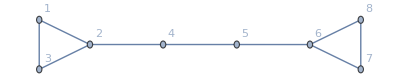

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
(*s = simplifyGraph[g];
GraphPlot3D[s]*)
```

```mathematica
EdgeQ[g,5<->4]
```

True

test mergeScore

```mathematica
ball1 = {{1,2,3},2};
ball2 = {{4,5,6},6};
mergeScore[ball1, ball2]
```

mergeScore[{{1,2,3},2},{{4,5,6},6}]

test simplifyGraph

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
h = simplifyGraph[g];
GraphPlot3D[h]
```

-Graphics-

0

-Graphics3D-

test smallestCircumBall

```mathematica
c1 = {0,0,0};
r1 = 1;
c2 = {0.1,0.5,0.6};
r2 = 0.4;
{c3,r3} = smallestCircumBall[{1,2,c1,r1},{1,2,c2,r2}]

a1 = Ball[c1,r1];
a2 = Ball[c2,r2];
a3 = Ball[c3,r3];

Graphics3D[{
	Opacity[0.5],
	Green,a1,
	Blue,a2,
	Red,a3}]
```

Part::partw: Part 5 of {1,2,{0,0,0},1} does not exist.

Part::partw: Part 5 of {1,2,{0.1,0.5,0.6},0.4} does not exist.

{1-0.3 (Max[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]+Min[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]),0.3 (Abs[Max[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]]+Abs[Min[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]])}

-Graphics3D-

```mathematica
a=Graph[{1<->2,1<->2,1<->3,4<->2}]
```

-Graphics-

```mathematica
b=EdgeList[a,1<->_]
```

{1<->2,1<->2,1<->3}

```mathematica
c=EdgeList[a,2<->_]
```

{1<->2,1<->2,4<->2}

```mathematica
d=Join[b,c]
```

{1<->2,1<->2,1<->3,1<->2,1<->2,4<->2}

```mathematica
e={1,2};
```

```mathematica
Select[d, (MemberQ[e, #⟦1⟧]&&!MemberQ[e, #⟦2⟧])||(!MemberQ[e, #⟦1⟧]&&MemberQ[e, #⟦2⟧]) &]
```

{1<->3,4<->2}

## Code

### Set working directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Excel Data

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"];
```

Import::nffil: File data\scoba12.xlsx not found during Import.

```mathematica
groundTruthTable = groundTruthTable[[1,;;,;;]];
trueJunctions = groundTruthTable[[;;,{4,5,6,10,19}]];
```

Part::partd: Part specification $Failed⟦1,1;;All,1;;All⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1;;All,1;;All⟧⟦1;;All,{4,5,6,10,19}⟧ is longer than depth of object.

### scoba12_small

#### Original

```mathematica
{thepoints,thelines,theradius,burnTime}=readSkel["scoba12_small_skel.ply"];
```

```mathematica
theSelectedLines = Select[thelines, (theradius⟦#⟦1⟧⟧+theradius⟦#⟦2⟧⟧)/2 > 1 &];
```

```mathematica
{theJ,theG}=initJG[thepoints,theSelectedLines,theradius,burnTime];
```

Initial graph built!

9000

8500

8000

7500

7000

6500

6000

5500

5000

4500

4000

3500

3000

2500

2000

1500

1000

500

0

simplified graph done!

Basic junctions computed!

```mathematica
{theJres,theGres,theJuncHistory}=computeCN2[theJ,theG,thepoints];
```

-1.

-0.927406

-0.923012

-0.885953

-0.882231

-0.841034

-0.837167

-0.826851

-0.818951

-0.815507

-0.81114

-0.795902

-0.79543

-0.787718

-0.780084

-0.779928

-0.77511

-0.774675

-0.769483

-0.723291

-0.720568

-0.717151

-0.714177

-0.705235

-0.693967

-0.6904

-0.674201

-0.662677

-0.652421

-0.630399

-0.617448

-0.616513

-0.595613

-0.59175

-0.577681

-0.577188

-0.576012

-0.566461

-0.565717

-0.56451

-0.559842

-0.55401

-0.550802

-0.539801

-0.531212

-0.523374

-0.512273

-0.508165

-0.497231

-0.49244

-0.486729

-0.476446

-0.448457

-0.435015

-0.422743

-0.388838

-0.367418

-0.331942

-0.26145

-0.250082

-0.235455

-0.223721

-0.221793

-0.216702

-0.155198

-0.144709

-0.0777584

-0.00389932

0.13888

0.140756

0.160506

0.160658

0.166603

0.194413

0.206864

0.243552

0.288351

0.28863

0.290579

0.29758

0.297626

0.363619

0.382713

0.383921

0.40369

0.521441

0.614904

0.623691

0.627949

0.656436

0.675

0.779915

0.827401

0.88111

0.896058

0.91138

```mathematica
Length[theJ]
Length[theJres]
Dimensions[theJuncHistory]
```

208

112

{96,2}

#### Dilation

```mathematica
{dPoints,dLines,dRadius,dBurnTime}=readSkel["scoba12_small_dilate_skel.ply"];
```

```mathematica
dSelectedLines = Select[dLines, (dRadius⟦#⟦1⟧⟧+dRadius⟦#⟦2⟧⟧)/2 > 2 &];
```

```mathematica
{dJ,dG}=initJG[dPoints,dSelectedLines,dRadius,dBurnTime];
```

Initial graph built!

5500

5000

4500

4000

3500

3000

2500

2000

1500

1000

500

0

simplified graph done!

Basic junctions computed!

```mathematica
{dJres,dGres,dJuncHistory}=computeCN2[dJ,dG,dPoints];
```

-0.970104

-0.950646

-0.888266

-0.865945

-0.861271

-0.857757

-0.856278

-0.854601

-0.852363

-0.851555

-0.840155

-0.838857

-0.817086

-0.816921

-0.791098

-0.769844

-0.759713

-0.757003

-0.752223

-0.747585

-0.741039

-0.718072

-0.71725

-0.680893

-0.636799

-0.625161

-0.600834

-0.589344

-0.526273

-0.512996

-0.5

-0.477258

-0.386638

-0.348607

-0.230611

-0.210107

-0.168166

-0.130713

-0.118446

-0.100226

-0.0854127

-0.0417349

-0.0225182

-0.0151317

-0.00483648

0.084882

0.115002

0.200939

0.29978

0.31398

0.574998

0.787291

0.828372

0.849854

```mathematica
Length[dJ]
Length[dJres]
Dimensions[dJuncHistory]
```

111

57

{54,2}